```mathematica
If[NumberQ[bQdef],None,Quit[]];
```

# RSD P22 functions

Alejandro Aviles (avilescervantes@gmail.com)
Compute P22(k) functions for HS models and LCDM   (set bLCDM=1 below)

```mathematica
SetDirectory[NotebookDirectory[]]
dir=SetDirectory[NotebookDirectory[]]<>"/";
Print["Running P22 functions"];
<<0_params.m
If[NumberQ[bQdef],None,<<0_folders.m];
```

/home/waco/Dropbox/RSDMG/SPT/AfterPaper/sMGPT_NoScreenings

Running P22 functions

suffix = F5z05_NoScreen

fR0 = -0.00001

OmegaM0 = 0.281, h = 0.697

redshift z = 0.5 , eta = -0.405465

Screenings off

## General parameters

```mathematica
PSLT=Import[outputdir<>"/PSL_"<>suffix<>".dat"];
PSL=Interpolation[PSLT];

fkTh=Import[outputdir<>"/fk_"<>suffix<>".dat"];
f0=fkTh[[2,2]];
Print["f(k=0)=",f0];
(*If[bLCDM==1,fk[k_]:=f0,fk=Interpolation[fkTh]];*)(* Assuming the MG model f[k=0]=f_LCDM. Does not work in DGP *)
fk=Interpolation[fkTh]

sizepk=Dimensions[PSLT][[1]];
Print["input PS points = ",sizepk,", kmin = ",PSLT[[1,1]],", kmax = ",PSLT[[sizepk,1]]];
fourpi2=4.Pi^2;
```

f(k=0)=0.733322

InterpolatingFunction[{{0.00001, 521.888}}, <>]

input PS points = 890, kmin = 0.00001, kmax = 521.888

## General functions (modify here for other models)

```mathematica
OmM[eta_]:=1/(1+(1-om)/om Exp[3eta]);
H[eta_]:=√(om Exp[-3eta]+(1-om));

f1[eta_]:=(2.-3./(2.(1.+(1-om)/om Exp[3.eta])));
f2[eta_]:=3./(2.(1.+(1-om)/om Exp[3.eta]));
invH0 =2997.92458 ;(* H_0^-1 in Mpc/h units *)


(* MODEL DEPENDENT FUNCTIONS *)
beta2=1/6;
nHS=1;
mass[eta_]:=1/invH0(1/(2 fR0))^(1/2)(om Exp[-3 eta]+4(1-om))^((2+nHS)/2)/(om+4(1-om))^((1+nHS)/2);
mu[eta_,k_]:=1+(2beta2 k^2)/(k^2+Exp[2 eta] mass[eta]^2) ; (*mu is from A(k) = 3/2 Subscript[Ω, m] H^2 μ *)
M1[eta_]:=3 mass[eta]^2;
M2[eta_]:=Sc(9./4)/invH0^2(1/fR0)^2(om Exp[-3. eta]+4.(1-om))^5/(om+4(1-om))^4;


PiF[eta_,k_]:=k^2/Exp[2. eta]+mass[eta]^2;
```

```mathematica
(*LogLinearPlot[{mu[0,k],mu[-1,k],1+1/3},{k,0.0001,100}]*)
```

## Second order functions differential equations

```mathematica
etainI=-4;
etafI=0.0;
etaini=etainI;

Dplusi=Exp[etaini];
dDplusi=Exp[etaini];


D2plusi=3Exp[2etaini]/7;
dD2plusi=6Exp[2etaini]/7;
etafinal=etaev;
Clear[kf,k1,k2]
sourcea[kf_,eta_]:=f2[eta] mu[eta,kf]
sourceb[kf_,k1_,k2_,eta_]:=f2[eta] (mu[eta,k1]+mu[eta,k2]-mu[eta,kf])
sourceFL[kf_,k1_,k2_,eta_]:=f2[eta] (((kf^2-k1^2-k2^2)/(2 k1^2)+(kf^2-k1^2-k2^2)/(2 k2^2))mu[eta,kf]-(kf^2-k1^2-k2^2)/(2 k1^2)mu[eta,k2]-((kf^2-k1^2-k2^2)/(2 k2^2))mu[eta,k1])
sourcedI[kf_,k1_,k2_,eta_]:=1/6 ((OmM[eta] H[eta])/(Exp[eta] invH0))^2 (kf^2 M2[eta])/( (kf^2 Exp[-2. eta]+mass[eta]^2) (k1^2 Exp[-2. eta]+mass[eta]^2) (k2^2 Exp[-2. eta]+mass[eta]^2) )

sourceA[kf_,k1_,k2_,eta_]:=sourcea[kf,eta]+sourceFL[kf,k1,k2,eta]-Sc sourcedI[kf,k1,k2,eta]

sysD2=ParametricNDSolve[{Af''[eta] +f1[eta]Af'[eta]-f2[eta] mu[eta,kf]Af[eta]==sourceA[kf,k1,k2,eta]Dpk1[eta]Dpk2[eta],Bf''[eta] +f1[eta]Bf'[eta]-f2[eta] mu[eta,kf]Bf[eta]==sourceb[kf,k1,k2,eta]Dpk1[eta]Dpk2[eta],Dpk1''[eta] +f1[eta]Dpk1'[eta]-f2[eta] mu[eta,k1]Dpk1[eta]==0,Dpk2''[eta] +f1[eta]Dpk2'[eta]-f2[eta] mu[eta,k2]Dpk2[eta]==0,Af'[etaini]==dD2plusi,Af[etaini]==D2plusi,Bf'[etaini]==dD2plusi,Bf[etaini]==D2plusi,Dpk1'[etaini]==Exp[etaini],Dpk1[etaini]==Exp[etaini],Dpk2'[etaini]==Exp[etaini],Dpk2[etaini]==Exp[etaini]},{Af,Bf,Dpk1,Dpk2},{eta,etainI,etafinal},{kf,k1,k2}]

unbarA:=Evaluate[Af/.sysD2]
unbarB:=Evaluate[Bf/.sysD2]
preDk1:=Evaluate[Dpk1/.sysD2]
preDk2:=Evaluate[Dpk2/.sysD2]
Dk1[k1_]:=preDk1[0.001,k1,0.001]
Dk2[k2_]:=preDk2[0.001,0.001,k2]


A[k12_,k1_,k2_]:=(unbarA[k12,k1,k2][etaev])/(3/7 preDk1[k12,k1,k2][etaev]preDk2[k12,k1,k2][etaev])

B[k12_,k1_,k2_]:=(unbarB[k12,k1,k2][etaev])/(3/7 preDk1[k12,k1,k2][etaev]preDk2[k12,k1,k2][etaev])

Aprime[k12_,k1_,k2_]:= D[(unbarA[k12,k1,k2][eta])/(3/7 preDk1[k12,k1,k2][eta]preDk2[k12,k1,k2][eta]),eta]/.eta->etaev
Bprime[k12_,k1_,k2_]:= D[(unbarB[k12,k1,k2][eta])/(3/7 preDk1[k12,k1,k2][eta]preDk2[k12,k1,k2][eta]),eta]/.eta->etaev

AprimeLCDM=Aprime[0.0001,0.0001,0.0001] (*Large scales value. For f(R) this is LCDM *)
ALCDM=A[0.00001,0.00001,0.00001]  (*Large scales value. For f(R) this is LCDM *)
```

{Af→ParametricFunction[<>],Bf→ParametricFunction[<>],Dpk1→ParametricFunction[<>],Dpk2→ParametricFunction[<>]}

0.00933252

1.00402

## Tables of k and p points

```mathematica
ttft=True;
<<0_tables.m
ttft=False;
```

Input kmin = 0.00001,  input kmax = 402.401

Output files log-k spaced: kmin = 0.001,  kmax = 1,  number of ks: 121

Inner integration pmin = 0.00001,  pmax = 16.,  number of ps: 183

## Plot linear PS

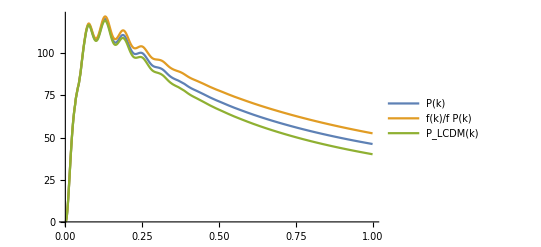

```mathematica
PSLCDMz0=Interpolation[Import[inputpk]];
Plot[{k^1.5PSL[k],k^1.5fk[k]/f0 PSL[k],k^1.5 PSL[0.0001]/PSLCDMz0[0.0001] PSLCDMz0[k]},{k,0.001,1},PlotLegends->{"P(k)","f(k)/f P(k)","P_LCDM(k)"}]
```

## INTEGRATE

## Define Kernels

```mathematica
(*bLCDM=1;*)
AngleEvQ[r_,x_]:=(x-r )/Sqrt[1+r^2-2. r x];

S2evQ[r_,x_]:=AngleEvQ[r,x]AngleEvQ[r,x]-1/3;

F2evQ[k_,r_,x_,A_,B_]:=0.5+3./14. A +(0.5-3./14. B)AngleEvQ[r,x]^2 +AngleEvQ[r,x]/2( Sqrt[1+r^2-2. r x]/r + r/Sqrt[1+r^2-2. r x] );

G2evQ[k_,r_,x_,A_,B_,Aprime_,Bprime_,fp_,fkminusp_]:=3./14. A (fp+fkminusp)/f0 + 3/14.Aprime/f0 +( 1./2 (fp+fkminusp) -  3./14. B(fp+fkminusp)-3/14.Bprime)*AngleEvQ[r,x]^2/f0 +AngleEvQ[r,x]/(2f0)(fkminusp Sqrt[1+r^2-2. r x]/r + fp r/Sqrt[1+r^2-2. r x] );


KF2sq[k_,r_,x_,A_,B_]:=2 r^2(F2evQ[k,r,x,A,B])^2;
KG2sq[k_,r_,x_,A_,B_,Aprime_,Bprime_,fp_,fkminusp_]:=2 r^2(G2evQ[k,r,x,A,B,Aprime,Bprime,fp,fkminusp])^2;
KF2G2[k_,r_,x_,A_,B_,Aprime_,Bprime_,fp_,fkminusp_]:=2 r^2 F2evQ[k,r,x,A,B]G2evQ[k,r,x,A,B,Aprime,Bprime,fp,fkminusp];



KPb2b1[k_,r_,x_,A_,B_]:=r^2F2evQ[k,r,x,A,B];
KPbs2b1[k_,r_,x_,A_,B_]:=r^2S2evQ[r,x]F2evQ[k,r,x,A,B];

KPb22[k_,r_,x_]:=1/2r^2 (1/2(1-PSL[k r]/PSL[k Sqrt[1+r^2-2 r x]])+1/2(1-PSL[k Sqrt[1+r^2-2 r x]]/PSL[k r]));

KPb2s2[k_,r_,x_]:=1/2r^2 (1/2(S2evQ[r,x]-2/3PSL[k r]/PSL[k Sqrt[1+r^2-2 r x]])+1/2(S2evQ[r,x]-2/3PSL[k Sqrt[1+r^2-2 r x]]/PSL[k r]));
KPbs22[k_,r_,x_]:=1/2r^2 (1/2(S2evQ[r,x]S2evQ[r,x]-4/9PSL[k r]/PSL[k Sqrt[1+r^2-2 r x]])+1/2(S2evQ[r,x]S2evQ[r,x]-4/9PSL[k Sqrt[1+r^2-2 r x]]/PSL[k r]));


KPb2theta[k_,r_,x_,A_,B_,Aprime_,Bprime_,fp_,fkminusp_]:=r^2G2evQ[k,r,x,A,B,Aprime,Bprime,fp,fkminusp];
KPbs2theta[k_,r_,x_,A_,B_,Aprime_,Bprime_,fp_,fkminusp_]:=r^2S2evQ[r,x]G2evQ[k,r,x,A,B,Aprime,Bprime,fp,fkminusp];


If[PTkernels==1||PTkernels==2,bLCDMkernels=0,bLCDMkernels=1];
If[PTkernels==3||PTkernels==5,Clear[fk];fk[k_]:=f0];
If[PTkernels==5||PTkernels==6,ALCDM=1;AprimeLCDM=0];

If[bLCDMkernels==0,Ah[k12_,k1_,k2_]:=A[k12,k1,k2],Ah[k12_,k1_,k2_]:=ALCDM]
If[bLCDMkernels==0,Bh[k12_,k1_,k2_]:=B[k12,k1,k2],Bh[k12_,k1_,k2_]:=ALCDM]
If[bLCDMkernels==0,Aprimeh[k12_,k1_,k2_]:=Aprime[k12,k1,k2],Aprimeh[k12_,k1_,k2_]:=AprimeLCDM]
If[bLCDMkernels==0,Bprimeh[k12_,k1_,k2_]:=Bprime[k12,k1,k2],Bprimeh[k12_,k1_,k2_]:=AprimeLCDM]





P22kernelsT[k_,r_,x_,A_,B_,Aprime_,Bprime_,fp_,fkminusp_]:={KF2sq[k,r,x,A,B],KG2sq[k,r,x,A,B,Aprime,Bprime,fp,fkminusp],KF2G2[k,r,x,A,B,Aprime,Bprime,fp,fkminusp],KPb2b1[k,r,x,A,B],KPbs2b1[k,r,x,A,B],KPb22[k,r,x],KPb2s2[k,r,x],KPbs22[k,r,x],KPb2theta[k,r,x,A,B,Aprime,Bprime,fp,fkminusp],KPbs2theta[k,r,x,A,B,Aprime,Bprime,fp,fkminusp]};
P22kernelsT[1,1,0.3,1,1,0,0,1,1];
NumQs=Length@P22kernelsT[1,1,0.3,1,1,0,0,1,1];
Print["Integrating ", NumQs, " kernels"];
```

MG kernels ON

Integrating 10 kernels

## Integrate

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"] (*This is for GL angular integration *)
kmax=PSLT[[sizepk,1]]
kmin=PSLT[[2,1]]
OutT={};
voidT={};
Do[AppendTo[OutT,voidT],{pp,1,NumQs}];

ta=AbsoluteTime[];
Do[
ki=kT[[koutin]];

Qp={};
Do[AppendTo[Qp,0],{pp,1,NumQs}];
QfunctionsB={};
Do[AppendTo[QfunctionsB,0],{pp,1,NumQs}];
QfunctionsA={};
Do[AppendTo[QfunctionsA,0],{pp,1,NumQs}];

PSLA=0;
rmax=kmax/ki;
rmin=kmin/ki;
Do[
p=pT[[pii]];
rr=p/ki;
PSLB=PSL[ki rr] ;
fp=fk[ki rr];


mumin=Max[-1.0,(1.+rr^2-rmax^2)/2./rr];
mumax=Min[1.0,(1.+rr^2-rmin^2)/2./rr];
If[rr≥0.5,mumax=0.5/rr];
Nx=10;
tGL=GaussianQuadratureWeights[Nx,mumin,mumax];
xGL=tGL[[All,1]];
wGL=tGL[[All,2]];

Do[
xv=xGL[[xii]];
w=wGL[[xii]];
KA=Ah[ki,ki rr,ki Sqrt[1+rr^2-2 rr xv]];
KB=Bh[ki,ki rr,ki Sqrt[1+rr^2-2 rr xv]];
KAprime=Aprimeh[ki,ki rr,ki Sqrt[1+rr^2-2 rr xv]];
KBprime=Bprimeh[ki,ki rr,ki Sqrt[1+rr^2-2 rr xv]];





fkminusp=fk[ki Sqrt[1+rr^2-2 rr xv]];
psl=PSL[ki Sqrt[1+rr^2-2 rr xv]];

QkernelsT=P22kernelsT[ki,rr,xv,KA,KB,KAprime,KBprime,fp,fkminusp];

Do[QfunctionsB[[pp]]=QfunctionsB[[pp]]+w*psl*QkernelsT[[pp]],{pp,1,NumQs}];


,{xii,1,Nx}];

deltar=(pT[[pii]]-pT[[pii-1]])/ki;

Do[Qp[[pp]]=Qp[[pp]]+(QfunctionsA[[pp]]*PSLA+QfunctionsB[[pp]]*PSLB)/2.*deltar,{pp,1,NumQs}];

QfunctionsA=QfunctionsB;
PSLA=PSLB;
QfunctionsB={};
Do[AppendTo[QfunctionsB,0],{pp,1,NumQs}];

,{pii,2,sizepT}];

Do[Qp[[pp]]=2 ki^3/fourpi2 *Qp[[pp]],{pp,1,NumQs}];
Do[OutT[[pp]]=Append[OutT[[pp]],{ki,Qp[[pp]]}],{pp,1,NumQs}];

If[koutin/10==Floor[koutin/10],Print[koutin,": k=",ki, ",  time= ",AbsoluteTime[]-ta]];

,{koutin,1,sizekT}]//AbsoluteTiming
```

402.401

0.0000101043

10: k=0.0016788,  time= 20.51892

20: k=0.00298538,  time= 40.99952

30: k=0.00530884,  time= 61.574829

40: k=0.00944061,  time= 82.0062

50: k=0.016788,  time= 102.58033

60: k=0.0298538,  time= 123.94496

70: k=0.0530884,  time= 144.43481

80: k=0.0944061,  time= 164.81304

90: k=0.16788,  time= 185.29466

100: k=0.298538,  time= 205.69185

110: k=0.530884,  time= 226.9887

120: k=0.944061,  time= 248.31752

{250.4071,Null}

```mathematica
NumQs
```

10

## Export

```mathematica
P22kernelsT[k_,r_,x_,A_,B_,Aprime_,Bprime_,fp_,fkminusp_]:={KF2sq[k,r,x,A,B],KG2sq[k,r,x,A,B,Aprime,Bprime,fp,fkminusp],KF2G2[k,r,x,A,B,Aprime,Bprime,fp,fkminusp],KPb2b1[k,r,x,A,B],KPbs2b1[k,r,x,A,B],KPb22[k,r,x],KPb2s2[k,r,x],KPbs22[k,r,x],KPb2theta[k,r,x,A,B,Aprime,Bprime,fp,fkminusp],KPbs2theta[k,r,x,A,B,Aprime,Bprime,fp,fkminusp]};
```

```mathematica
str="# 1.k[h/Mpc] 2.Pdeltadelta22  3.Pthetatheta22  4.Pdeltatheta22  5.Pb2b1   6.Pbs2b1    7.Pb22   8.Pb2s2  9.Pbs22   10.Pb2theta   11.Pbs2theta"  ;
preExpT=Table[{OutT[[1]][[ii,1]], OutT[[1]][[ii,2]],OutT[[2]][[ii,2]],OutT[[3]][[ii,2]],OutT[[4]][[ii,2]],OutT[[5]][[ii,2]],OutT[[6]][[ii,2]],OutT[[7]][[ii,2]],OutT[[8]][[ii,2]],OutT[[9]][[ii,2]],OutT[[10]][[ii,2]]},{ii,1,Dimensions[OutT[[1]]][[1]]}];
Dimensions[%]
ExpT=PrependTo[preExpT,str];
Dimensions[%]
filetoexport=outputdir<>"/P22functions_"<>suffix<>".dat";
Export[filetoexport,ExpT]
Print["P22 functions saved in file ",filetoexport];
Print[" "];
```

{121,11}

{122}

P22functions_F6z05.dat

P22 functions saved in file P22functions_F6z05.dat